## Zestaw 6

Katarzyna Sowa

## 1N

Zbudowano wielomian interpolacyjny oparty na nastepujacych danych:

```mathematica
XY={{0.06250,0.687959},{0.187500,0.073443},{0.312500,-0.517558},{0.437500,-1.077264},{0.562500,-1.600455},{0.687500,-2.080815},{0.812500,-2.507266},{0.935700,-2.860607}};
```

```mathematica
Lagrange[XY_,rozm_]:=
Module[{n=rozm-1,wyn,suma=0,resz,X,Y},
X =Transpose[XY]_⟦1⟧;
Y = Transpose[XY]_⟦2⟧; 
Do[wyn = 1; 
Do[ resz = Which[ j==k, 1,
j≠k,(x - X_⟦j+1⟧)/(X_⟦k+1⟧-X_⟦j+1⟧) ]; 
wyn= wyn*resz; ,{j,0,n,1}]; 
suma = suma+ Y_⟦k+1⟧*wyn; ,{k,0,n,1}]; 

Return[Print["Wielomian interpolacyjny: "];
Expand[suma]]; ];
```

Wielomian interpolacyjny:

1.00104-5.03245 x+0.348127 x^2+0.199569 x^3+3.03844 x^4-6.80247 x^5+6.28258 x^6-2.05026 x^7

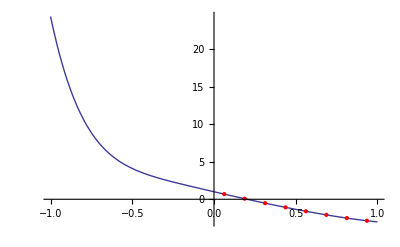

```mathematica
y=Lagrange[XY,8]
Show[Plot[y,{x,-1,1}],ListPlot[XY,PlotStyle->{Red,PointSize[Medium]}]]
```

## 2N

```mathematica
f[x_]:=(x^2-1)(Sinh[x])^3;
```

```mathematica
(*a,b przedzial*)
```

```mathematica
Sieczne[a_,b_,iter_]:=Module[{x=Table[0&,{iter}],x1,x2,i, h=Random[Real,{a,b}]} ,

Print["Warunek na zgodnosc znakow pochodnych: ",f'[h]*f''[h]];
If[f'[h]*f''[h]>=0,
x1=a;
Print["x1= ",x1];
Print["x2=", x2=N[x1-f[x1]/(f[b]-f[x1])(b-x1)]];
x_⟦1⟧=x1;
x_⟦2⟧=x2;
For[i=3,i≤iter,i++,
x_⟦i⟧=x_⟦i-1⟧-(f[x_⟦i-1⟧](x_⟦i-1⟧-x_⟦i-2⟧))/(f[x_⟦i-1⟧]-f[x_⟦i-2⟧])
]Print["Miejsce zerowe z dokladnoscia do 10: x= ",x_⟦iter⟧]
(*jesli nie*),
x1=b;
Print["x1= ",x1];
Print["x2=", x2=N[x1-f[x1]/(f[a]-f[x1])(a-x1)]];
x_⟦1⟧=x1;
x_⟦2⟧=x2;
For[i=3,i≤iter,i++,
x_⟦i⟧=x_⟦i-1⟧-(f[x_⟦i-1⟧](x_⟦i-1⟧-x_⟦i-2⟧))/(f[x_⟦i-1⟧]-f[x_⟦i-2⟧])
]Print["Miejsce zerowe z dokladnoscia do 10: x= ",x_⟦iter⟧]
]Return[];];
```

```mathematica
Sieczne[0.00001,0.999,23]
```

Warunek na zgodnosc znakow pochodnych: 0.287852

x1= 0.00001

x2=0.00001

Miejsce zerowe z dokladnoscia do 10: x= 2.48511×10^-8

```mathematica
Sieczne[0.001,0.09,23]
```

Warunek na zgodnosc znakow pochodnych: 0.00002377

x1= 0.001

x2=0.000999877

Miejsce zerowe z dokladnoscia do 10: x= 2.48492×10^-6

```mathematica
Sieczne[0.25,0.879,23]
```

Warunek na zgodnosc znakow pochodnych: 0.674136

x1= 0.25

x2=0.204727

Miejsce zerowe z dokladnoscia do 10: x= 0.000536427

```mathematica
Sieczne[0.000125,0.000999,23]
```

Warunek na zgodnosc znakow pochodnych: 5.63917×10^-11

x1= 0.000125

x2=0.000123284

Miejsce zerowe z dokladnoscia do 10: x= 3.07981×10^-7

Wartosc miejsca zerowego zmienia sie w zaleznosci od punktow przedzialu.

## 3N

```mathematica
Show[Plot[f[x],{x,-5,5}],Plot[f'[x],{x,-5,5},PlotStyle->Green],Plot[f''[x],{x,-5,5},PlotStyle->Red]]
```

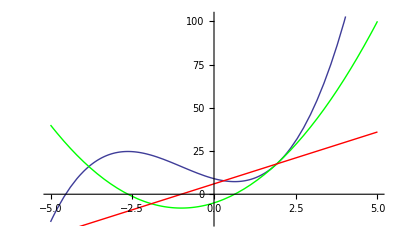

```mathematica
f[x_]:=x^3+3 x^2-5x+9;
```

```mathematica
f[x_]=x^3+3 x^2-5x+9;
Newt[z_]=z-f[z]/f'[z];
ListDensityPlot[Table[-Length[FixedPointList[Newt,N[a+b I],30]],{b,-2,2,.01},{a,-2,2,.01}],Mesh->False,MeshRange->{{-2,2},{-2,2}}]
```

## 4N

```mathematica
f[x_]:=x^3+3 x^2-5x+9;
```

```mathematica
f[x_]:=3 x^2;
```

```mathematica
Halley[z_]:=z-(2*f[z]*f'[z])/(2(f'[z])^2-f[z]*f''[z]);
```

```mathematica
ListDensityPlot[Table[-Length[FixedPointList[Halley,N[a+b ⅈ],20]],{b,-2,2,.01},{a,-2,2,.01}],Mesh->False,MeshRange->{{-2,2},{-2,2}}]
```

## 6N

Rozwiazac uklad rownan:
2 x^2+y^2=2
(x - 1/2)^2+(y-1)^2=1/4
W funkcji Mathematici FindRoot domyslnie uzywana jest metoda Newtona znajdowania rozwiazania ukladow rownan nieliniowych:

```mathematica
FindRoot[{2 x^2+y^2==2,(x-1/2)^2+(y-1)^2==1/4},{{x,1},{y,1}}]
```

{x→0.879121,y→0.674013}